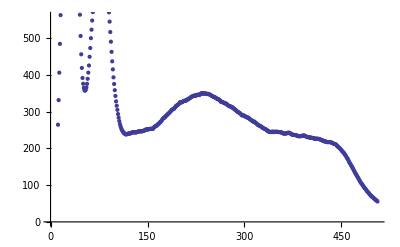

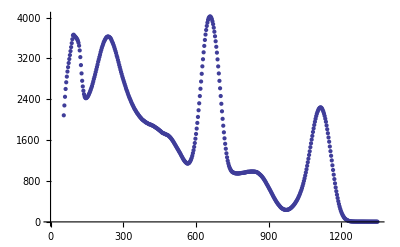

```mathematica
Data = Import["C:\\Users\\Jackson\\Documents\\GitHub\\AdvanceLab\\Gama_Spectroscopy\\data\\cs-137.tsv"][[26;;,{2,3}]];
p1 = ListPlot[MovingAverage[Data[[1;;-500]],30]]
Data = Import["C:\\Users\\Jackson\\Documents\\GitHub\\AdvanceLab\\Gama_Spectroscopy\\data\\unknown.tsv"][[26;;,{2,3}]];
p2= ListPlot[MovingAverage[Data[[1;;-500]],30]]
(*Show[p1,p2];*)
```